```mathematica
Ln1=4;
Ln2=1;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+γ))^(l1+l2)(γ/(2+γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*γ^c/(γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*γ^c/(γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

Marginals (l1<L1) (Change l2 for l1 to get the opposite)

```mathematica
PM1[l1_,L2_,c_,γ_]:=Sum[P1[l1,l2,c,γ],{l2,0,L2-1}]+P2[l1,L2,c,γ]
```

Marginals (l=L) (l2=L2) (Change l1 for l2 to get opposite)

```mathematica
PM2[L1_,L2_,c_,γ_]:=Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]+P3[L1,L2,c,γ]
```

Mutual Information

```mathematica
IN[L1_,L2_,c_,γ_]:=Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]/(PM1[l1,L2,c,γ]*PM1[l2,L1,c,γ])],{l1,0,L1-1}],{l2,0,L2-1}]+Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]/(PM1[l1,L2,c,γ]*PM2[L1,L2,c,γ])],{l1,0,L1-1}]+Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]/(PM1[l2,L1,c,γ]*PM2[L2,L1,c,γ])],{l2,0,L2-1}]+P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]/(PM2[L1,L2,c,γ]*PM2[L2,L1,c,γ])]
```

Perfect Clock

```mathematica
Pc1[l1_,l2_,t_]:=Exp[-2*t]*t^(l1+l2)/(l1!l2!)
Pc2[l1_,L2_,t_]:=t^l1/(l1!)*Exp[-t]*(1-Exp[-t]*Sum[t^l2/(l2!),{l2,0,L2-1}])
Pc3[L1_,L2_,t_]:=1-Sum[Sum[Pc1[l1,l2,t],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[Pc2[l1,L2,t],{l1,0,L1-1}]-Sum[Pc2[l2,L1,t],{l2,0,L2-1}]
```

Marginals (l1<L1)

```mathematica
PcM1[l1_,L2_,t_]:=Sum[Pc1[l1,l2,t],{l2,0,L2-1}]+Pc2[l1,L2,t];
```

Marginals(l1=L1)

```mathematica
PcM2[L1_,L2_,t_]:=Sum[Pc2[l2,L1,t],{l2,0,L2-1}]+Pc3[L1,L2,t];
```

Mutual info

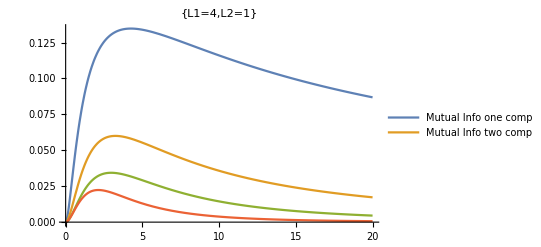

```mathematica
Plot[{IN[4,1,1,1/τ],IN[4,1,2,2/τ],IN[4,1,3,3/τ],IN[4,1,4,3/τ]},{τ,0,20},PlotLabel->{"L1=4,L2=1"}, PlotLegends->{"Mutual Info one comp","Mutual Info two comp"}]
```

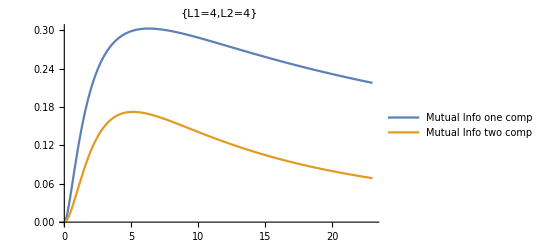

```mathematica
Plot[{IN[4,4,1,1/τ],IN[4,4,2,2/τ]},{τ,0.1,23},PlotLabel->{"L1=4,L2=4"}, PlotLegends->{"Mutual Info one comp","Mutual Info two comp"}]
```

```mathematica
maxMI=Flatten[Evaluate@Table[FindArgMax[Simplify[IN[4,1,c,c/t]],{t,1,5}],{c,1,5}]]
maxMI2=Flatten[Evaluate@Table[FindMaxValue[Simplify[IN[4,1,c,c/t]],{t,1,5}],{c,1,5}]];
maxM13=Evaluate@Table[FindMaximum[Simplify[IN[4,1,c,c/t]],{t,1,5}],{c,1,5}];
Join[maxMI,maxMI2,2]
```

{{4.25125},{3.24241},{2.96511},{2.83674},{2.76301}}

Join::headsd: Expression {0.134751, 0.0600291, 0.0343628, 0.0223595, 0.0157444} at position 2 is expected to have head List for all expressions at level 2.

Join[{{4.25125},{3.24241},{2.96511},{2.83674},{2.76301}},{0.134751,0.0600291,0.0343628,0.0223595,0.0157444},2]

FindArgMax::nrnum: The function value « 13 » + « 1 »/« 1 »\ « 1 » - 1/6\ (6\ (1 - 2\ Times[« 2 »]^c + (c\ Power[« 2 »])^c) + (Times[« 3 »] + Times[« 3 »] + Times[« 3 »])\ c ! + « 1 » « 1 » (Times[« 3 »] + « 1 »)\ « 1 »/(-1 + c) !)\ Log[6\ (6\ (1 + Times[« 2 »] + Power[« 2 »]) + Times[« 2 »] + Times[« 2 »] + Times[« 2 »]/« 1 » !)/(6 - 6\ Power[« 2 »] + Power[« 2 »]\ Plus[« 3 »])\ (6 - 6\ Power[« 2 »] + 1.\ Power[« 2 »]\ Power[« 2 »]\ Plus[« 2 »]\ Power[« 2 »]\ Plus[« 2 »])] is not a real number at {t} = {1.}.

Flatten::flpi: Levels to be flattened together in {c, 1, 5} should be lists of positive integers.

FindArgMax::nrnum: The function value « 13 » + « 1 »/« 1 »\ « 1 » - 1/6\ (6\ (1 - 2\ Times[« 2 »]^c + (c\ Power[« 2 »])^c) + (Times[« 3 »] + Times[« 3 »] + Times[« 3 »])\ c ! + « 1 » « 1 » (Times[« 3 »] + « 1 »)\ « 1 »/(-1 + c) !)\ Log[6\ (6\ (1 + Times[« 2 »] + Power[« 2 »]) + Times[« 2 »] + Times[« 2 »] + Times[« 2 »]/« 1 » !)/(6 - 6\ Power[« 2 »] + Power[« 2 »]\ Plus[« 3 »])\ (6 - 6\ Power[« 2 »] + 1.\ Power[« 2 »]\ Power[« 2 »]\ Plus[« 2 »]\ Power[« 2 »]\ Plus[« 2 »])] is not a real number at {t} = {1.}.

General::stop: Further output of FindArgMax :: nrnum will be suppressed during this calculation.

Flatten::flpi: Levels to be flattened together in {c, 1, 5} should be lists of positive integers.

General::stop: Further output of Flatten :: flpi will be suppressed during this calculation.

Flatten[FindArgMax[Simplify[IN[4,1,c,c/t]],{t,1,5}],{c,1,5}]

```mathematica
MatrixForm[maxMI]
```

(4.25125
3.24241
2.96511
2.83674
2.76301)

```mathematica
ListPlot[[maxMI,maxMI2]]
```

Part::pkspec1: The expression {{4.25125}, {3.24241}, {2.96511}, {2.83674}, {2.76301}} cannot be used as a part specification.

ListPlot⟦{{4.25125},{3.24241},{2.96511},{2.83674},{2.76301}},{0.134751,0.0600291,0.0343628,0.0223595,0.0157444}⟧